```mathematica
ClearAll["Global`*"]
```

Value Declaration

## Value from Field tests

```mathematica
dist = {0,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1,1.1};
prssi={-49,-82.5,-85,-88,-99,-99,-104,-99,-105,-105,-106,-105};
snr1 ={9,9,8,8,4,4,3,-1,-3,-5,-7,-9};
totPacket1 = {100/100,99/100,100/100,98/100,98/100,99/100,95/100,95/100,93/100,88/100,75/100,23/100};
```

## Values for Formulas

```mathematica
Subscript[h, b]=Subscript[h, m]=1;
f =868.1;
Subscript[Pt, W]=100*10^-3;
Subscript[Pt, dBm]=10*Log10[Subscript[Pt, W]]+30;
Subscript[Pt, dBw]=10*Log10[Subscript[Pt, W]];
Subscript[Gt, dBi]=Subscript[Gr, dBi]=3.43;
BW=125000;
xLee=43.5;
Subscript[L, 0]=89;
NF=6;
```

Formulas Declaration

## Field Test

```mathematica
rssi =Transpose[{dist,prssi}];
pdr=Transpose[{dist,totPacket1}];
snr = Transpose[{dist,snr1}];
paraSNR = Fit[snr,{1,kx,kx^2,kx^3,kx^4,kx^5},kx];
paraRSSI= Fit[rssi,{1,kx},kx];
paraPDR= Fit[pdr,{1,1,kx,kx^2,kx^3,kx^4,kx^5,kx^6,kx^7,kx^8},kx];
```

## Hata Model Open Area

```mathematica
xa[h_]:=(1.1*Log10[f]-0.7)*h-(1.56*Log10[f]-0.8);
aa=69.55+26.161*Log10[f]-13.82*Log10[Subscript[h, b]]-xa[Subscript[h, m]];
bb=44.9-6.55*Log10[Subscript[h, b]];
cc=40.94+4.78*(Log10[f])^2-18.33*Log10[f];
LHata[d_]:=aa+bb*Log10[d]-cc;

Subscript[PrHata, dBm][d_]:=Subscript[Pt, dBm]+Subscript[Gt, dBi]+Subscript[Gr, dBi]-LHata[d];
Subscript[PrHata, dBw][d_]:=Subscript[Pt, dBw]+Subscript[Gt, dBi]+Subscript[Gr, dBi]-LHata[d];

intersection1Hata={d,-117.67}/.NSolve[Subscript[PrHata, dBm][d]==-117.6,d];
intersection2Hata={d,-148}/.NSolve[Subscript[PrHata, dBm][d]==-148,d];
```

## LEE Model

```mathematica
Subscript[F, 1][h_]:=(h/30.48)^2;
Subscript[F, 2][G_]:=G/4;
Subscript[F, 3][h_]:=(h/3);
Subscript[F, 4][f_,n_]:=(f/900)^-n;
Subscript[F, 5][G_]:=G/1;
Subscript[F, 0]=Subscript[F, 1][1]*Subscript[F, 2][Subscript[Gr, dBi]-2.15]*Subscript[F, 3][1]*Subscript[F, 4][868.1,2.5]*Subscript[F, 5][Subscript[Gt, dBi]-2.15];
LtotalLEE[d_]:=Subscript[L, 0]+xLee*Log10[d]-10*Log10[Subscript[F, 0]];
Subscript[PrLEE, dBm][d_]:=Subscript[Pt, dBm]+Subscript[Gt, dBi]+Subscript[Gr, dBi]-LtotalLEE[d];
Subscript[PrLEE, dBw][d_]:=Subscript[Pt, dBw]+Subscript[Gt, dBi]+Subscript[Gr, dBi]-LtotalLEE[d];
intersection1LEE={d,-117.67}/.NSolve[Subscript[PrLEE, dBm][d]==-117.6,d];
intersection2LEE={d,-148}/.NSolve[Subscript[PrLEE, dBm][d]==-148,d];
```

## Noise Signal

```mathematica
CG[SF_]:=2.5*SF;
Subscript[N, dBm][spreadFactor_]:=-174+NF+10*Log10[125000]+CG [spreadFactor];
```

Plot

```mathematica
plotrangerssi={{0.075,1.2},{-30,-150}};
distance = 2;
```

## Propagation Loss

### Estimated

#### Hata Model Open Area

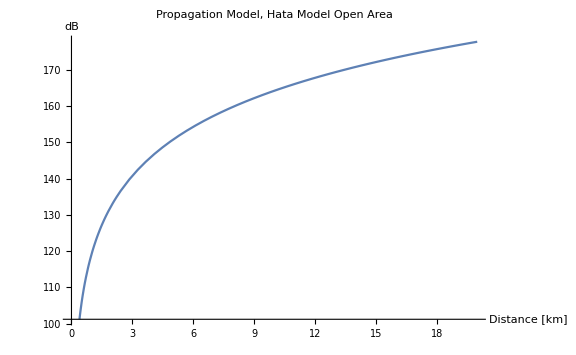

```mathematica
Plot[LHata[d],{d,0,20},AxesLabel->{"Distance [km]","dB"},PlotLabel->"Propagation Model, Hata Model Open Area",ImageSize->Large]
```

#### LEE Model

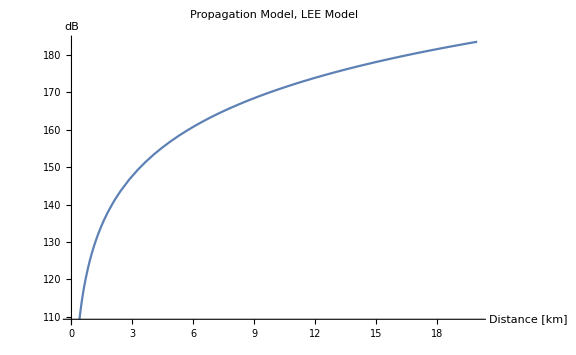

```mathematica
Plot[LtotalLEE[d],{d,0,20},AxesLabel->{"Distance [km]","dB"},ImageSize->Large,PlotLabel->"Propagation Model, LEE Model"]
```

## Received Signal Strength Indicator (RSSI)

### Estimated

#### Hata Model Open Area

```mathematica
Rasterize[Plot[{Subscript[PrHata, dBm][d],-117.67,-148},{d,0,20},AxesLabel->{"Distance [km]","RSSI [dBm]"},ImageSize->Large,Epilog->{PointSize[Large],Black,Point[intersection1Hata],Point[intersection2Hata]},PlotLabel-> "Recieved Signal Strength Indicator, Hata Model Open Area",PlotLegends->{"P_r(Recieved Power)","Spread Factor = 7", "Spread Factor = 12"}]
]
Rasterize[LogLinearPlot[{Subscript[PrHata, dBm][d],-117.67,-148},{d,0,20},AxesLabel->{"Distance [km]","RSSI [dBm]"},ImageSize->Large,PlotLabel-> "Recieved Signal Strength Indicator, Hata Model Open Area",PlotLegends->{"P_r(Recieved Power)","SF = 7", "SF = 12"}]
]
```

-Graphics-

-Graphics-

#### LEE Model

```mathematica
Rasterize[Plot[{Subscript[PrLEE, dBm][d],-117.67,-148},{d,0,17},AxesLabel->{"Distance [km]","RSSI [dBm]"},ImageSize->Large,Epilog->{PointSize[Large],Black,Point[intersection1LEE],Point[intersection2LEE]},PlotLabel-> "Recieved Signal Strength Indicator, LEE Model",PlotLegends->{"P_r(Recieved Power)","Spread Factor = 7", "Spread Factor = 12"}]]
Rasterize[LogLinearPlot[{Subscript[PrLEE, dBm][d],-117.67,-148},{d,0,17},AxesLabel->{"Distance [km]","RSSI [dBm]"},
ImageSize->Large,PlotLabel-> "Recieved Signal Strength Indicator, LEE Model",
PlotLegends->{"P_r(Recieved Power)","SF = 7", "SF = 12"}]]
```

-Graphics-

-Graphics-

### Measured

```mathematica
Rasterize[Show[
ListPlot[rssi],
Plot[paraRSSI,{kx,0,1.1},PlotStyle->{Dashed,RGBColor[0.27,0.49,1.]},PlotLegends->{"Approximated Function, Field Tests"}],
Plot[{Subscript[PrHata, dBm][d],-117.67,-148},{d,0,1.7},PlotStyle->RGBColor[1.,0.48,0.17],PlotLegends->{"RSSI Hata Model"}],
Plot[{Subscript[PrLEE, dBm][d],-117.67,-148},{d,0,1.7},PlotStyle->RGBColor[0.,0.56,0.26],PlotLegends->{"RSSI LEE Model"}],
Plot[-117.67,{d,0,1.7},PlotLegends->{"RSSI Limit, SF = 7"},PlotStyle->RGBColor[0.77,0.22,0.]],
Plot[-148,{d,0,1.7},PlotLegends->{"RSSI Limit, SF = 12"},PlotStyle->RGBColor[0.25,0.19,0.]],
PlotRange->Automatic,
ImageSize->Large,
AxesLabel->{"Distance [km]","RSSI [dBm]"},
PlotLabel-> "Recieved Signal Strength Indicator"
]
]
```

-Graphics-

```mathematica
Rasterize[Show[
LogLinearPlot[paraRSSI,{kx,0,1.1},PlotStyle->{Dashed,RGBColor[0.27,0.49,1.]},PlotRange->plotrangerssi],
ListLogLinearPlot[rssi],
LogLinearPlot[{Subscript[PrHata, dBm][d],-117.67,-148},{d,0,distance},PlotStyle->RGBColor[1.,0.48,0.17],PlotLegends->{"RSSI Hata Model"},PlotRange->plotrangerssi],
LogLinearPlot[{Subscript[PrLEE, dBm][d]},{d,0,distance},AxesLabel->{"Distance [km]","dB"},
ImageSize->Large,PlotLabel-> "Recieved Signal Power, LEE Model",PlotStyle->RGBColor[0.,0.56,0.26],
PlotLegends->{"RSSI LEE Model"},PlotRange->plotrangerssi
],
LogLinearPlot[-117.67,{x,0,distance},PlotStyle->RGBColor[0.77,0.22,0.],PlotLegends->{"RSSI Limit, SF = 7"},PlotRange->plotrangerssi],
LogLinearPlot[-148,{x,0,distance},PlotStyle->RGBColor[0.25,0.19,0.],PlotLegends->{"RSSI Limit, SF = 12"},PlotRange->plotrangerssi],
ImageSize->Large,
AxesLabel->{"Distance [km]","RSSI [dBm]"},
PlotLabel-> "Recieved Signal Strength Indicator"
]
]
```

-Graphics-

```mathematica
nlm=LinearModelFit[rssi,Exp[-x],x]//Normal;
Rasterize[Show[
(*LogLinearPlot[paraRSSI,{kx,0,1.1},PlotStyle->{Dashed,RGBColor[0.27,0.49,1.]},PlotRange->plotrangerssi]*)
LogLinearPlot[nlm,{x,0,1.2},PlotStyle->{RGBColor[0.27,0.49,1.]},PlotRange->plotrangerssi,PlotLegends->{"Approximated RSSI Function"}],
ListLogLinearPlot[rssi],
LogLinearPlot[{Subscript[PrHata, dBm][d],-117.67,-148},{d,0,distance},PlotStyle->RGBColor[1.,0.48,0.17],PlotLegends->{"RSSI Hata Model"},PlotRange->plotrangerssi],
LogLinearPlot[{Subscript[PrLEE, dBm][d]},{d,0,distance},AxesLabel->{"Distance [km]","dB"},
ImageSize->Large,PlotLabel-> "Recieved Signal Power, LEE Model",PlotStyle->RGBColor[0.,0.56,0.26],
PlotLegends->{"RSSI LEE Model"},PlotRange->plotrangerssi
],
LogLinearPlot[-117.67,{x,0,distance},PlotStyle->RGBColor[0.77,0.22,0.],PlotLegends->{"RSSI Limit, SF = 7"},PlotRange->plotrangerssi],
LogLinearPlot[-148,{x,0,distance},PlotStyle->RGBColor[0.25,0.19,0.],PlotLegends->{"RSSI Limit, SF = 12"},PlotRange->plotrangerssi],
ImageSize->Large,
AxesLabel->{"Distance [km]","RSSI [dBm]"},
PlotLabel-> "Recieved Signal Strength Indicator"
]
]
```

-Graphics-

## Signal-to-Noise Ratio (SNR)

### Estimated

#### Hata Model Open Area

```mathematica
SignalToNoise[SpreadFactor_,dist_] :=Subscript[PrHata, dBm][dist]-Subscript[N, dBm][SpreadFactor];
Rasterize[LogLinearPlot[{SignalToNoise[7,dist],SignalToNoise[12,dist],-7.5,-20},
{dist,0,10},
PlotLegends->{"SNR, Spread Factor = 7","SNR, Spread Factor = 12","SNR Demodulator, Spread Factor = 7","SNR Demodulator, Spread Factor = 12"},
ImageSize->Large,
PlotLabel->"SNR Estimation, Hata Model Open Area",
AxesLabel->{"Distance [km]","SNR [dB]"}
]
]
```

-Graphics-

#### LEE Model

```mathematica
SignalToNoise[SpreadFactor_,dist_] :=Subscript[PrLEE, dBm][dist]-Subscript[N, dBm][SpreadFactor];
Rasterize[LogLinearPlot[{SignalToNoise[7,dist],SignalToNoise[12,dist],-7.5,-20},
{dist,0,10},
PlotLegends->{"SNR, Spread Factor = 7","SNR, Spread Factor = 12","SNR Demodulator, Spread Factor = 7","SNR Demodulator, Spread Factor = 12"},
ImageSize->Large,
PlotLabel->"SNR Estimation, LEE Model",
AxesLabel->{"Distance [km]","SNR [dB]"}
]
]
```

-Graphics-

### Measured

```mathematica
Rasterize[Show[ListPlot[snr],
Plot[paraSNR,{kx,0,1.2},PlotLegends->{"Approximated Function, Field Tests"},PlotStyle->{Dashed,RGBColor[0.27,0.49,1.]}],
Plot[-7.5,{kx,0,1.5},PlotStyle->RGBColor[1.,0.48,0.17],PlotLegends->{"SNR Limit, SF = 7"}],
Plot[-20,{kx,0,1.5},PlotStyle->RGBColor[0.,0.56,0.26],PlotLegends->{"SNR Limit, SF = 12"}],
PlotLabel-> "Signal to Noise Ratio",
ImageSize->Large,
PlotRange->Automatic,
AxesLabel->{ "Distance [km]","SNR [dB]"}
]
]
```

-Graphics-

## Packet Error Rate (PER)

### Measured

```mathematica
Rasterize[Show[ListLogLinearPlot[pdr],
LogLinearPlot[paraPDR,{kx,0,20},PlotLegends->{"Approximated Function, Field Tests"},PlotStyle->{Dashed,RGBColor[0.27,0.49,1.]}],
PlotLabel-> "Packet Delivery Rate, Field Tests",
AxesLabel-> {"Distance [km]","PDR"},
ImageSize->Large
]
]
```

-Graphics-

## Confidence Intervals

### SNR

These values are taken from the receiving module based on 100 sent packets.

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
snr1100={-8,-9,-10,-9,-10,-10,-9,-9,-11,-9,-8,-10,-9,-8,-11,-9,-9-8,-6,-7,-6,-5,-7,-7};
snr1000={-7,-7,-7,-9,-7,-7,-8,-9,-8,-6,-11,-8,-9,-8,-7,-8,-8,-7,-8,-8,-7,-8,-7,-7,-6,-5,-6,-6,-6,-7,-6,-8,-6,-7,-7,-7,-7,-7,-7,-8,-7,-7,-7,-5,-6,-5,-5,-6,-5,-5,-5,-5,-4,-5,-6,-4,-5,-6,-5,-5,-4,-5,-6,-4,-7,-6,-5,-6,-6,-6,-5,-5,-5,-8,-7};
snr800 = {-9,-4,-8,-2,-11,-10,-5,-1,-3,-5,-1,-2,-1,-1,-3,-2,-1,-1,-1,0,0,-1,-2,-3,-3,-3,-2,-3,-2,-2,-3,-2,-3,-2,-2,-2,-2,-2,-2,-1,-2,-2,-2,-2,-2,-3,-3,-4,-4,-6,-6,-7,-8,-6,-8,-2,-3,-2,-3,-4,-3,-2,-4,-7,-5,-4,-5,-6,-7,-7,-6,-5,-6,-5,-6,-7,-5,-6,-7,-7,-8,-7,-7,-7,-7,-7,-7,-6,-8,-7,-7,-7,-8};
snr900 = {3,-4,1,1,0,1,1,0,1,1,0,1,1,2,2,2,0,-2,-2,-5,-7,-6,-6,-6,-5,-4,-4,0,-2,2,3,1,1,2,0,-6,-10,-9,-10,-9,-10,-9,-9,-6,-6,-7,-4,-7,-4,-8,-7,-9,-10,-10,-8,0,-1,1,0,1,0,0,-1,0,0,0,0,1,0,0,0,0,0,-2,-5,-4,-4,-3,-3,-3,2,-7,1,1,1,2,-4,-7};
snr700={-6,-5,-5,-7,-2,-4,1,0,-2,-3,-3,-3,-2,-4,-2,3,0,3,2,-4,-1,0,-2,-4,-2,-1,-1,-3,-5,-4,-1,-4,0,0,0,0,-5,-2,-1,-4,1,-4,-7,-7,-9,-1,-4,1,-2,-1,2,3,4,1,1,1,5,4,2,6,0,-3,1,4,2,3,1,3,4,3,4,3,5,1,7,3,-2,0,7,5,0,1,0,2,0,-2,0,-10,-1,-1,-3,-4,-3,-3,-3};
snr600={2,2,3,3,3,4,4,4,5,3,3,4,4,6,5,4,5,4,4,5,5,-1,5,6,6,7,7,7,7,6,7,7,6,7,7,7,6,7,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,6,6,6,5,6,7,6,6,6,5,6,6,6,5,6,5,6,6,6,6,5,5,5,5,5,5,6,6,6,5,5,6,5,5,5,4,5,5,6,6};
snr500={2,2,0,2,4,4,3,4,5,6,5,5,5,6,5,6,6,5,5,5,6,5,5,5,5,5,5,5,6,5,5,5,5,5,5,4,4,5,5,5,5,5,6,5,5,5,5,5,5,7,7,6,6,7,6,6,6,6,7,6,6,6,4,5,4,3,5,4,4,2,2,3,5,6,5,5,7,7,6,7,6,6,6,6,6,7,6,6,6,6,6,5,6,6,6,6,6,6,2};
snr400={5,8,0,-3,-4,-6,-6,-1,1,3,0,0,0,1,-1,-1,-1,0,1,-1,2,3,-2,6,1,3,5,5,7,5,6,5,5,5,5,3,4,4,3,3,3,5,4,6,5,6,6,6,6,7,6,6,6,7,7,7,6,7,6,6,6,6,6,7,6,5,6,6,7,8,8,7,7,7,8,8,7,7,7,7,7,7,7,7,6,6,6,7,7,7,7,8,8,7,7,7,7,7};
snr300={9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,9,9,9,9,9,9,2,9,9,9,9,9,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,9,9,9,9,9,8,9,9,9,9,9,9,9,9,9,9,9,8};
snr200={9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,9,9,9,9,9,9,8,9,9,9,9,9,9,8,8,9,9,9,8,8,9,9,9,9,8,8,8,9,8,9,8,9,8,9,9,9,9,10,9,9,8,9,9,9,9,9,9,8,9,9,9,9,9,9,9,9,9,9,9,9,9};
snr100={9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,5,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9};
snr5={9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9};

(*Confidence interval calculations: dB converted to linear -> MeanCI -> converted to dB scale*)
s5=10*Log10[MeanCI[10^(snr5/10)]];
s100=10*Log10[MeanCI[10^(snr100/10)]];
s200=10*Log10[MeanCI[10^(snr200/10)]];
s300=10*Log10[MeanCI[10^(snr300/10)]];
s400=10*Log10[MeanCI[10^(snr400/10)]];
s500=10*Log10[MeanCI[10^(snr500/10)]];
s600=10*Log10[MeanCI[10^(snr600/10)]];
s700=10*Log10[MeanCI[10^(snr700/10)]];
s800=10*Log10[MeanCI[10^(snr800/10)]];
s900=10*Log10[MeanCI[10^(snr900/10)]];
s1000=10*Log10[MeanCI[10^(snr1000/10)]];
s1100=10*Log10[MeanCI[10^(snr1100/10)]];
```

```mathematica
TableForm[
{{snr1[[1]],{s5}}
,{snr1[[2]],{s100}}
,{snr1[[3]],{s200}}
,{snr1[[4]],{s300}}
,{snr1[[5]],{s400}}
,{snr1[[6]],{s500}}
,{snr1[[7]],{s600}}
,{snr1[[8]],{s700}}
,{snr1[[9]],{s800}}
,{snr1[[10]],{s900}}
,{snr1[[11]],{s1000}}
,{snr1[[12]],{s1100}}},
TableHeadings->{{"0 Meters","100 Meters","200 Meters","300 Meters","400 Meters","500 Meters","600 Meters","700 Meters","800 Meters","900 Meters","1000 Meters","1100 Meters"},{"Blynk App. SNR Value","Confidence Interval 95%"}}]
```

| Blynk App. SNR Value | Confidence Interval 95%
0 Meters | 9 | 8.98892 | 9.03343
100 Meters | 9 | 8.90842 | 9.01973
200 Meters | 8 | 8.83409 | 8.97545
300 Meters | 8 | 8.81358 | 8.98389
400 Meters | 4 | 5.03464 | 5.88107
500 Meters | 4 | 5.06365 | 5.50602
600 Meters | 3 | 5.36454 | 5.81874
700 Meters | -1 | -0.182678 | 1.31344
800 Meters | -3 | -4.06357 | -3.13074
900 Meters | -5 | -1.77228 | -0.538244
1000 Meters | -7 | -6.57615 | -5.96921
1100 Meters | -9 | -9.31172 | -7.58534

#### RSSI

```mathematica
prssi5 = {-48,-48,-48,-49,-48,-48,-48,-48,-48,-49,-49,-50,-49,-49,-49,-49,-49,-49,-49,-49,-50,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-48,-49,-49,-49,-49,-49,-49,-49,-48,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-48,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-50,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49,-49};
prssi100={-80,-79,-81,-80,-80,-80,-79,-79,-79,-79,-79,-78,-79,-79,-79,-79,-79,-80,-80,-80,-80,-81,-82,-81,-80,-81,-81,-81,-81,-80,-81,-81,-81,-81,-82,-81,-80,-79,-79,-80,-80,-81,-81,-81,-80,-80,-80,-79,-79,-78,-80,-79,-80,-81,-79,-80,-80,-79,-78,-80,-78,-79,-78,-79,-80,-79,-80,-79,-79,-79,-79,-80,-80,-80,-80,-80,-80,-79,-79,-79,-78,-77,-77,-77,-78,-77,-78,-77,-78,-78,-76,-77,-77,-77,-78,-79,-78,-79,-80};
prssi200={-83,-81,-83,-83,-82,-81,-81,-82,-82,-82,-82,-82,-82,-82,-82,-83,-81,-81,-82,-81,-82,-82,-82,-82,-82,-82,-83,-83,-83,-84,-84,-84,-84,-84,-84,-83,-84,-83,-83,-83,-85,-86,-85,-86,-85,-85,-87,-85,-85,-85,-85,-86,-85,-85,-85,-85,-86,-86,-85,-87,-86,-84,-84,-86,-85,-85,-85,-85,-87,-86,-86,-85,-85,-85,-86,-86,-85,-85,-86,-85,-85,-85,-84,-85,-84,-85,-86,-84,-85,-84,-85,-85,-84,-85,-85,-84,-84,-85,-85,-85};
prssi300={-89,-89,-90,-89,-88,-88,-88,-88,-89,-89,-89,-88,-89,-88,-88,-88,-89,-89,-88,-89,-89,-90,-89,-88,-88,-89,-89,-90,-90,-94,-95,-88,-87,-87,-86,-86,-87,-87,-87,-87,-87,-88,-87,-87,-86,-87,-87,-86,-87,-87,-87,-87,-88,-88,-88,-89,-88,-88,-87,-88,-87,-86,-87,-87,-87,-88,-87,-87,-88,-87,-87,-88,-88,-88,-88,-88,-88,-87,-88,-87,-88,-88,-88,-87,-88,-88,-88,-88,-89,-87,-88,-87,-88,-88,-88,-87,-87,-88};
prssi400={-99,-94,-104,-105,-106,-105,-106,-104,-104,-101,-104,-104,-103,-103,-105,-104,-104,-104,-103,-104,-102,-101,-104,-99,-102,-102,-99,-97,-95,-99,-97,-99,-99,-99,-100,-100,-100,-100,-101,-100,-101,-99,-100,-97,-99,-98,-98,-97,-97,-97,-97,-98,-98,-96,-97,-97,-98,-97,-98,-97,-97,-97,-97,-98,-97,-97,-97,-94,-93,-97,-96,-96,-95,-96,-96,-97,-97,-96,-97,-96,-98,-98,-98,-98,-97,-96,-96,-96,-96,-96,-96,-96,-96,-96,-97,-97,-96,-97};
prssi500={-102,-102,-104,-102,-101,-100,-101,-100,-100,-98,-98,-99,-98,-98,-99,-96,-97,-97,-99,-99,-98,-98,-98,-98,-97,-98,-98,-98,-98,-98,-98,-98,-98,-99,-99,-99,-100,-100,-98,-100,-99,-98,-99,-98,-98,-100,-98,-100,-98,-97,-97,-96,-97,-96,-97,-97,-98,-97,-96,-98,-97,-97,-100,-99,-100,-101,-98,-100,-100,-101,-102,-101,-99,-98,-98,-98,-97,-96,-96,-96,-96,-96,-96,-98,-96,-96,-98,-98,-98,-98,-98,-98,-97,-98,-98,-97,-98,-98,-102};
prssi600={-106,-105,-106,-106,-106,-106,-103,-104,-105,-105,-106,-106,-105,-106,-106,-103,-104,-101,-103,-105,-104,-104,-104,-105,-105,-105,-104,-106,-106,-106,-105,-106,-104,-103,-104,-104,-105,-105,-105,-106,-103,-106,-107,-107,-105,-102,-102,-101,-102,-102,-101,-101,-101,-103,-104,-103,-100,-102,-102,-98,-105,-105,-103,-100,-103,-101,-103,-102,-101,-102,-100,-102,-100,-103,-97,-102,-105,-105,-97,-99,-104,-104,-104,-103,-105,-106,-104,-107,-105,-106,-106,-106,-106,-106,-106};
prssi700={-102,-101,-101,-101,-101,-100,-101,-100,-100,-102,-100,-100,-100,-98,-99,-100,-100,-100,-100,-99,-99,-104,-100,-96,-96,-96,-96,-96,-96,-96,-96,-96,-96,-96,-97,-97,-98,-96,-97,-97,-98,-97,-98,-97,-98,-98,-97,-97,-98,-97,-96,-96,-96,-97,-96,-96,-97,-97,-97,-97,-98,-98,-97,-97,-97,-97,-98,-98,-99,-98,-98,-97,-98,-99,-99,-98,-98,-98,-98,-99,-99,-98,-98,-98,-99,-99,-98,-98,-98,-98,-99,-99,-98,-99,-98};
prssi800={-101,-105,-102,-103,-101,-102,-103,-102,-102,-103,-102,-103,-102,-102,-102,-102,-103,-105,-105,-105,-105,-105,-106,-105,-104,-105,-105,-103,-105,-102,-101,-102,-102,-101,-102,-106,-106,-106,-106,-106,-106,-106,-106,-105,-105,-106,-105,-106,-105,-106,-106,-106,-106,-106,-107,-103,-105,-103,-103,-103,-103,-104,-104,-104,-104,-104,-103,-103,-103,-103,-103,-103,-103,-105,-106,-105,-105,-105,-105,-105,-102,-106,-103,-106,-105,-106,-105,-106,-102,-103,-102,-103,-102};
prssi900={-106,-105,-105,-104,-106,-106,-103,-103,-105,-104,-104,-104,-104,-104,-105,-104,-104,-104,-104,-103,-103,-103,-104,-104,-104,-104,-104,-104,-103,-104,-104,-104,-105,-105,-104,-104,-103,-104,-104,-104,-104,-104,-104,-104,-104,-104,-104,-105,-104,-105,-105,-105,-105,-105,-105,-104,-104,-104,-105,-104,-105,-104,-104,-105,-105,-105,-105,-105,-105,-105,-105,-105,-106,-105,-105,-106,-105,-106,-105,-105,-105,-105,-105,-105,-105,-105,-105,-105};
prssi1000={-105,-106,-105,-105,-105,-105,-105,-105,-106,-105,-106,-105,-105,-105,-105,-106,-106,-105,-105,-105,-105,-105,-105,-105,-105,-105,-105,-105,-105,-106,-105,-105,-105,-105,-105,-105,-105,-105,-105,-105,-104,-105,-104,-105,-105,-105,-105,-105,-105,-105,-105,-105,-105,-105,-105,-105,-105,-105,-105,-106,-105,-105,-105,-105,-105,-104,-105,-105,-105,-106,-105,-105,-105,-104,-105};
prssi1100={-105,-105,-105,-105,-105,-105,-105,-105,-105,-105,-105,-105,-105,-104,-104,-104,-104,-104,-105,-104,-104,-105,-104};
```

```mathematica
(*Confidence interval calculations: dB converted to linear -> MeanCI -> converted to dB scale*)
p5=10*Log10[MeanCI[10^(prssi5/10)]];
p100=10*Log10[MeanCI[10^(prssi100/10)]];
p200=10*Log10[MeanCI[10^(prssi200/10)]];
p300=10*Log10[MeanCI[10^(prssi300/10)]];
p400=10*Log10[MeanCI[10^(prssi400/10)]];
p500=10*Log10[MeanCI[10^(prssi500/10)]];
p600=10*Log10[MeanCI[10^(prssi600/10)]];
p700=10*Log10[MeanCI[10^(prssi700/10)]];
p800=10*Log10[MeanCI[10^(prssi800/10)]];
p900=10*Log10[MeanCI[10^(prssi900/10)]];
p1000=10*Log10[MeanCI[10^(prssi1000/10)]];
p1100=10*Log10[MeanCI[10^(prssi1100/10)]];
```

```mathematica
TableForm[
{{prssi[[1]],{p5}}
,{prssi[[2]],{p100}}
,{prssi[[3]],{p200}}
,{prssi[[4]],{p300}}
,{prssi[[5]],{p400}}
,{prssi[[6]],{p500}}
,{prssi[[7]],{p600}}
,{prssi[[8]],{p700}}
,{prssi[[9]],{p800}}
,{prssi[[10]],{p900}}
,{prssi[[11]],{p1000}}
,{prssi[[12]],{p1100}}},
TableHeadings->{{"0 Meters","100 Meters","200 Meters","300 Meters","400 Meters","500 Meters","600 Meters","700 Meters","800 Meters","900 Meters","1000 Meters","1100 Meters"},{"Blynk App. RSSI Value","Confidence Interval 95%"}}]
```

| Blynk App. RSSI Value | Confidence Interval 95%
0 Meters | -49 | -48.9813 | -48.8284
100 Meters | -82.5 | -79.4641 | -78.9367
200 Meters | -85 | -84.1446 | -83.4829
300 Meters | -88 | -88.011 | -87.5974
400 Meters | -99 | -98.4299 | -97.4418
500 Meters | -99 | -98.4055 | -97.8184
600 Meters | -104 | -103.758 | -102.546
700 Meters | -99 | -98.1438 | -97.5464
800 Meters | -105 | -104.061 | -103.388
900 Meters | -105 | -104.576 | -104.259
1000 Meters | -106 | -105.127 | -104.946
1100 Meters | -105 | -104.848 | -104.414